## TemplateRandomSemicircularGrid-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (10-Nov-2012)) loaded Sat 10 Nov 2012 15:11:05
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 134 cells in the tissue.

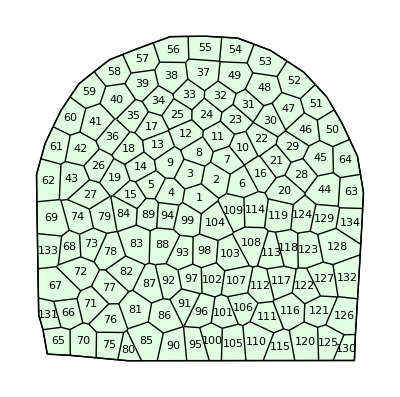

```mathematica
q=TemplateRandomSemicircularGrid[60, 100, 5];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True]
```